```mathematica
f=(x-I)(x-1-I)//ComplexExpand
f=x^2-(1+2I)x-(1-I)//ComplexExpand
f//TraditionalForm
f//Factor//TraditionalForm
Roots[f==0, x]//ComplexExpand
```

-1+ⅈ (1-2 x)-x+x^2

-1+ⅈ (1-2 x)-x+x^2

x^2-x+ⅈ (1-2 x)-1

(x-(1+ⅈ)) (x-ⅈ)

x==ⅈ||x==1+ⅈ

```mathematica
g[x_] := x^2-(1+I)x+(2+2I)
g[I+1]
```

2+2 ⅈ

```mathematica
1/Sqrt[9-x^2//Expand]
```

1/(√(9-x^2))

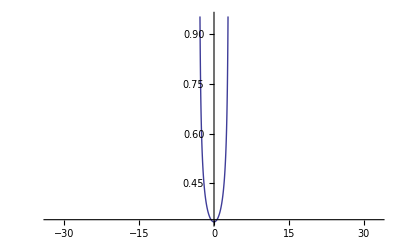

```mathematica
Plot[1/(√(9-x^2)),{x,-32.76,32.76}]
```

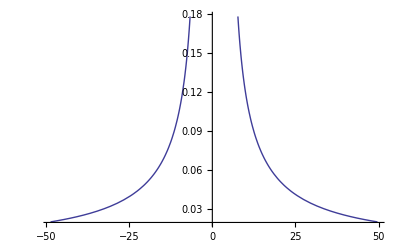

```mathematica
Plot[1/(√(-20-x+x^2)),{x,-48.64,49.64}]
```

```mathematica
Plot[1/(√((-5+x) (4+x))),{x,-48.64,49.64}]
```

-Graphics-

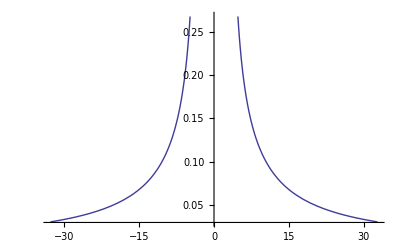

```mathematica
Plot[1/(√(-9+x^2)),{x,-32.76,32.76}]
```

```mathematica
Minimize[2x^2+4x,{x}]
```

{-2,{x→-1}}

```mathematica
Minimize[3 x+x^2,{x}]
```

{-9/4,{x→-3/2}}

```mathematica
HornerForm[3 x+x^2,{x-1}]
```

3 x+x^2

```mathematica
9-x^2≥0
```

9-x^2≥0

```mathematica
Reduce[x^2-x-20≥0,{x}]
```

x≤-4||x≥5

```mathematica
(x+I)(x-I)(x+(1+I))(x-(1+I))//ComplexExpand//TraditionalForm
```

x^4+x^2+ⅈ (-2 x^2-2)

```mathematica
Roots[(x+1)(x^2-x+3)==0,x]
```

x==-1||x==1/2 (1-ⅈ √11)||x==1/2 (1+ⅈ √11)

```mathematica
Maximize[-2x^2+24x,x]
```

{72,{x→6}}

```mathematica
Minimize[800-10x+0.25x^2,x]
```

{700.,{x→20.}}

```mathematica
f=((x+1)/(x^3-8))1/3
```

(1+x)/(3 (-8+x^3))

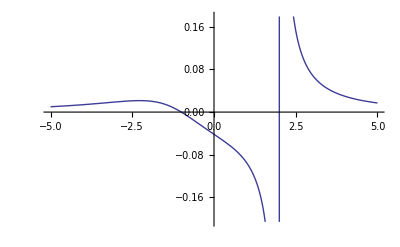

```mathematica
Plot[(1+x)/(3 (-8+x^3)),{x,-5,5}]
```

```mathematica
f=x^3+8;
Factor[f]//TraditionalForm
Roots[f==0,x]//ComplexExpand
```

(x+2) (x^2-2 x+4)

x==-2||x==1-ⅈ √3||x==1+ⅈ √3

```mathematica
x^6-64//Factor//TraditionalForm
```

(x-2) (x+2) (x^2-2 x+4) (x^2+2 x+4)

```mathematica
(2x-1)(x+1)^2(x-I)(x+I)//Expand//TraditionalForm
```

2 x^5+3 x^4+2 x^3+2 x^2-1

```mathematica
PolynomialQuotientRemainder[x^3-x^2+2,x+1,x]//TraditionalForm
```

{x^2-2 x+2,0}

```mathematica
(24*5-8)/(24*5)//N
```

0.933333

```mathematica
24*5
```

120

```mathematica
64-4*17
```

-4

```mathematica
(x-(1+3I))(x-(1-3I))(x-2)//Expand//TraditionalForm
```

x^3-4 x^2+14 x-20

```mathematica
Roots[I x^2-2x+I==0,x]//TraditionalForm
```

x==-ⅈ-ⅈ √2∨x==ⅈ √2-ⅈ

```mathematica
(x-I)(x-1-I)//Expand//TraditionalForm
```

x^2-(1+2 ⅈ) x-(1-ⅈ)